# Polish Prefix Grammars, Type Systems, and Travesties --- Revision 7

## Brian Beckman 14 June 2012; 23 Sept 2021

## OVERVIEW

Mathematica supports an extremely easy and straightforward way to generate parsers and other syntax-directed tools like test generators for languages in Polish Prefix Form (PPF). In (our version of) this form, each term in the grammar has a unique leading head symbol. Arities of functional forms are fixed. Punctuation is not needed because the head immediately dictates how many tokens to consume for arguments For example, f x y z is f[x, y, z] transcribed to our punctuation-free PPF. The head is f, a non-terminal in the grammar. The expansion of f in the grammar specifies that f requires three arguments, x, y, and z. These are meta-syntactic variables, standing for arbitrary utterances in the grammar, not for specific terms.

The following are easy in PPF: general parsing and parser generation (utterances to trees), antiparsing (travesties: random but syntactically valid utterances) unparsing (trees to utterances). We illustrate using the famous game “Wff-n-Proof” as a motivating example. Then we move on to type systems, a-la Benjamin C. Pierce, using the same PPF grammars.

Any language that can be transcribed into PPF can enjoy the techniques presented in this paper. We promote the idea that it might be worth the effort to transcribe some complicated syntax like C++, Python, or Haskell, into PPF to ease the work of downstream language-processing tools like parsers and test generators.

(Wff-n-Proof: http://www.wffnproof.com, http://books.google.com/books?id=xwC6SgAACAAJ&dq=Wff-n-Proof&hl=en&sa=X&ei=LWXoT4KlIKKo2wXZ5YnaCQ&ved=0CEIQ6AEwAQ)

### Preliminaries

```mathematica
<<Utilities`CleanSlate`
```

You’ll need the following packages on your Mathematica $Path if you don’t mention their explicit locations. The following shows explicit locations where I put them on a Linux system:

```mathematica
<<"~/Dropbox/MMA/Packages/JacquardProlog.m"
<<"~/Dropbox/MMA/logic.m"
<<"~/Dropbox/MMA/Packages/Jacquard.m"
```

## POLISH PREFIX GRAMMARS

Polish prefix grammars are of the form [non-terminal] [some-fixed-number-of-arguments]. Such grammars are easy to parse, and it’s even easy to automatically generate parsers for them from a specification of the grammar. Our goal here is not to be sophisticated with syntax, but to explore type systems.

## DEFINITIONS

The following shows one way to build simplified language tools in Mathematica. Forward references to later definitions are written in non-bold italics. Definitions are written in bold-italics.

Let a grammar be a function from non-terminal symbols to productions, each of which is a suit (ordered collection with no duplicates, aka permutation) of alternatives. Alternatives are ordered for the convenience of pairing (zipping) them with travesty-generation probabilities; logically, alternatives are unordered, i.e., a set rather than a suit.

The productions of a context-free grammar pertain anywhere in an utterance without regard to preceding or following input. Such grammars are the only ones of interest, here.

A production is a suit of alternatives.

Each alternative is a list, sequence, array (all synonyms for an ordered collection, duplicates allowed) of terms. The terms must match, in both order and form, the terms in utterances.

A term is either a terminal symbol or a non-terminal symbol.

A terminal symbol is a literal, usually a String or a Number, that must match exactly a token appearing in the input.

A token is a string or number, for example, containing an atomic utterance of the language of interest. In Wff-n-Proof, our motivating example, a token is a single character.

A non-terminal symbol recurses back into the grammar. It’s always of Mathematica type (i.e., Head) Symbol.

The start symbol is the special, distinguished name and symbol Start, not available for other uses.

## MOTIVATING EXAMPLE: WFF-N-PROOF

The following is an example of a Polish-prefix, context-free grammar from the famous game “Wff-n-Proof.”

```mathematica
ClearAll[P,Wff,Proposition,Unary,Binary,T,nonTerminalsFromGrammar,terminalsFromGrammar];
```

We represent suits, sets, bags, and lists as lists in Mathematica.

### P = suit of productions = our grammar: Global Variable for our motivating example

NOTE: We never refer to Global Variables in function bodies. That’s dangerous because their values may change willy-nilly. Instead, all our functions take all data through parameters. Our Global Variables represent specific examples like Wff-n-Proof, and those Global Variables may appear as actual arguments when calling functions.

P is a list (as a suit of productions) of lists (as alternatives, i.e., as sequences of terms).

A Wff is either a Proposition, a Unary, or a Binary:

```mathematica
P[Wff]=({{Proposition}, {Unary}, {Binary}});
```

A Proposition is any one of the four terminal constants p, q, r, s.

```mathematica
P[Proposition]= ({{"p"}, {"q"}, {"r"}, {"s"}});
```

A Unary --- the language has only one Unary --- is a terminal N followed by a Wff.

```mathematica
P[Unary]=({{"N", Wff}});
```

The language has four Binaries:

C is Conditional
A is not And, it’s OR!
K is Konjunction (it’s AND)
E is Equivalence

```mathematica
P[Binary]=({{"C", Wff, Wff}, {"A", Wff, Wff}, {"K", Wff, Wff}, {"E", Wff, Wff}});
```

The magical Start symbol is just a Wff:

```mathematica
P[Start]={{Wff}};
```

Double-check:

```mathematica
??P
```

### NT = set of non-terminals for Wff-n-Proof: Global Variable

“DownValues” sniffs the domain (non-terminals) of a tabular function-definition like P.

```mathematica
DownValues[P]//TableForm
```

HoldPattern[P[Binary]]:>{{C,Wff,Wff},{A,Wff,Wff},{K,Wff,Wff},{E,Wff,Wff}}
HoldPattern[P[Proposition]]:>{{p},{q},{r},{s}}
HoldPattern[P[Start]]:>{{Wff}}
HoldPattern[P[Unary]]:>{{N,Wff}}
HoldPattern[P[Wff]]:>{{Proposition},{Unary},{Binary}}

How about a pretty display for the domain? Terminals are in dark red, non-terminals in dark blue. Lists are green boxes. Lists of lists are doubled green boxes. This visual notation does not distinguish lists as suits, lists as sets, lists as sequences, or lists as bags. Rules have orange boxes on the left and light-yellow boxes on the right..18The following displays the rules above.

```mathematica
Module[{d=DownValues[P]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules
```

Binary | C
Wff
Wff
A
Wff
Wff
K
Wff
Wff
E
Wff
Wff
Proposition | p
q
r
s
Start | Wff
Unary | N
Wff
Wff | Proposition
Unary
Binary

```mathematica
ClearAll[nonTerminalsFromGrammar];
nonTerminalsFromGrammar[ps_]:=#[[1,1,1]]&/@DownValues[ps]
```

```mathematica
(NT=nonTerminalsFromGrammar[P])//InputForm
```

{Binary, Proposition, Start, Unary, Wff}

### T = set of terminals for Wff-n-Proof: Global Variable

The terminals in a grammar is the complement of the non-terminals against the set of all symbols, which is the union of all the right-hand sides of the productions.

```mathematica
ClearAll[allSymbols];
allSymbols[ps_]:=Union@Flatten[#[[2]]&/@DownValues[ps]]
```

In gridExpression, terminals are in a light-yellow background, non-terminals in a purple background; gridExpression is a visual FullForm, so it shows the Head List explicitly, whereas gridRules exhibits lists as colored boxes without the explicit Head List.

```mathematica
allSymbols[P]//gridExpression
```

| A
 | C
 | E
 | K
 | N
 | p
List | q
 | r
 | s
 | Binary
 | Proposition
 | Unary
 | Wff

InputForm is another way to visualize data. It adds back in the double quotes around Strings.

```mathematica
allSymbols[P]//InputForm
```

{"A", "C", "E", "K", "N", "p", "q", "r", "s", Binary, Proposition, Unary, 
 Wff}

```mathematica
ClearAll[terminalsFromGrammar];
terminalsFromGrammar[ps_]:=
Complement[
allSymbols @ ps,
nonTerminalsFromGrammar @ ps]
```

InputForm shows the double quotes of Strings.

```mathematica
(T=terminalsFromGrammar @ P)//InputForm
```

{"A", "C", "E", "K", "N", "p", "q", "r", "s"}

## ANTI-PARSING: SYNTAX-DRIVEN TRAVESTIES

### Inject Probabilities into the Grammar

Transform each alternative (sequence of terms) into a list of rules (that is, a Jacquard object): one rule for the probability of choosing the alternative in a travesty and another rule for the original alternative itself. Generate the probabilities with a given function that maps the alternatives to a parallel, isocardinal (zippable) list. The orders of the alternatives and of the probabilities are important only for Zip, even though the alternatives are, notionally, a set.

```mathematica
ClearAll[injectGenerationProbabilities];
injectGenerationProbabilities[
grammar_,
probsFromAlternatives_]:=
Module[{newTable,nonTerminals=nonTerminalsFromGrammar@grammar},
Scan[(* Scan is like Map, but just for side-effects *)
Function[nonTerminal,
With[{
alternatives=grammar[nonTerminal],
probabilities=probsFromAlternatives[grammar[nonTerminal]]},
newTable[nonTerminal]=(* side-effect this definition *)
Zip[probabilities, alternatives,
Function[{prob,alt},
{"probability"->prob,"alternative"->alt}]]]],
nonTerminals];(* scan over this list *)
newTable]; (* return the side-effected table *)
```

The following function assigns equal probabilities to every element of a list. It’s the default. Use something else if you have better estimates of appropriate probabilities. We’ll see an example of that in BPTProbabilities below.

```mathematica
ClearAll[equiProbabilities];
equiProbabilities[list_List]:=
With[{l=Length@list},Table[N[1/l],{l}]]
```

### iP = set of probabilized productions: Global Variable

Productions (headed by non-terminals) with injected probabilities.

```mathematica
ClearAll[iP];
(iP=injectGenerationProbabilities[P,equiProbabilities]);
```

Examine them (DownValues doesn’t Evaluate its arguments by default, so we must).

```mathematica
TableForm/@DownValues[Evaluate[iP]]
```

{HoldPattern[newTable$772037[Binary]]:>{{probability→0.25,alternative→{C,Wff,Wff}},{probability→0.25,alternative→{A,Wff,Wff}},{probability→0.25,alternative→{K,Wff,Wff}},{probability→0.25,alternative→{E,Wff,Wff}}},HoldPattern[newTable$772037[Proposition]]:>{{probability→0.25,alternative→{p}},{probability→0.25,alternative→{q}},{probability→0.25,alternative→{r}},{probability→0.25,alternative→{s}}},HoldPattern[newTable$772037[Start]]:>{{probability→1.,alternative→{Wff}}},HoldPattern[newTable$772037[Unary]]:>{{probability→1.,alternative→{N,Wff}}},HoldPattern[newTable$772037[Wff]]:>{{probability→0.333333,alternative→{Proposition}},{probability→0.333333,alternative→{Unary}},{probability→0.333333,alternative→{Binary}}}}

Something a bit more pretty to look at? In here, “probability” and “alternative” are strings as keys in lookup tables as rules. They’re not terminals in the grammar, and you can tell that they’re not because they’re inside orange boxes, where the keys of rules always go in gridRules.

```mathematica
Module[{d=DownValues[Evaluate[iP]]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules
```

Binary | probability | 0.25
alternative | C
Wff
Wff
probability | 0.25
alternative | A
Wff
Wff
probability | 0.25
alternative | K
Wff
Wff
probability | 0.25
alternative | E
Wff
Wff
Proposition | probability | 0.25
alternative | p
probability | 0.25
alternative | q
probability | 0.25
alternative | r
probability | 0.25
alternative | s
Start | probability | 1.
alternative | Wff
Unary | probability | 1.
alternative | N
Wff
Wff | probability | 0.333333
alternative | Proposition
probability | 0.333333
alternative | Unary
probability | 0.333333
alternative | Binary

### Choose From Alternatives

A function from probabilized alternatives to a particular choice, given an input die roll.

If there is only one alternative, choose it. Notice that we access the key “alternative” in the lookup table (Jacquard object) by applying the rules (/., ReplaceAll) that implement the object. ReplaceAll fills the role of dot in Jacquard’s version of lightweight polymorphism, the part of object-oriented programming that Jacquard exploits.

```mathematica
ClearAll[chooseFromAlternatives];
chooseFromAlternatives[{probabilizedAlternative_},dieRoll_]:="alternative"/.probabilizedAlternative;
```

If there are many, pick the first whose cumulative probability is greater than or equal to the dieRoll. Track the cumulative probability by decrementing the dieRoll by each non-cumulative probability as we recurse down the alternatives. More scalable is Walker’s method of aliases, but cumulation is good enough for small cases.

```mathematica
chooseFromAlternatives[{probabilizedAlternative_,rest___},dieRoll_]:=
With[{p="probability"/.probabilizedAlternative},
If[dieRoll<p,
(* then *)"alternative"/.probabilizedAlternative,
(* else *)chooseFromAlternatives[{rest},dieRoll-p]]];
chooseFromAlternatives[badArgs___]:=Throw[{"CHOOSE:BADARGS: ",{badArgs}}];
```

### generateSentences [ probabilizedGrammar, groundTerm, terminalSymbols, recursionLimit:100 ]

The ground term is the term to force when the recursion limit is exceeded. The default recursion limit is 100. 500 is a useful value for this limit, too.

#### chainExpansion: helper

It’s debatable whether to have a symbol like debugPrint for Print debugging, or to use Block[{Print=Identity},...] to switch off printing.

```mathematica
ClearAll[debugPrint];
debugPrint=Identity; (* Set it to Print when debugging, to Identity when not debugging. *)
```

Iterate down the terms, randomly choosing a branch to explore.

```mathematica
ClearAll[chainExpansion];
```

Case: exhausted the production:

```mathematica
chainExpansion[iP_,groundTerm_,T_,production:{},sentence_,
i_,iLim_]:=Module[{},
debugPrint[<|"branch"->"exhausted","i"->i,"production"->production,"sentence"->sentence|>];
sentence];
```

Case: we have a term in the production:

```mathematica
chainExpansion[iP_,gd_,T_,
production:{term_,rest___},
sentence_,i_,iLim_]/;(i<iLim):=
Module[{},
(* terminal symbol *)
If[MemberQ[T,term],
Module[{subtrees,result},
(* handle something like "if Term then Term else Term" *)
subtrees=
If[MemberQ[T,#],{#},
chainExpansion[iP,gd,T,{#},{},i+1,iLim]]&/@{rest};
result=Join[sentence,{term},Flatten[subtrees,1]];
debugPrint[<|"branch"->"term","i"->i,"prodn"->production,"term"->term,"rest"->{rest},"sub"->subtrees,"res"->result|>];
result],
(* non-terminal symbol *)
Module[{choice=chooseFromAlternatives[iP[term],RandomReal[]],
replacement,result}, replacement=chainExpansion[iP,gd,T,choice,{},i+1,iLim];
result=Join[sentence,replacement];
debugPrint[<|"branch"->"nterm","i"->i,"prodn"->production,"term"->term,"rest"->{rest},"choice"->choice,"repl"->replacement,"res"->result|>];
result
]]];
```

Case: exceeded the recursion limit:

```mathematica
chainExpansion[iP_,gd_,T_,production_,sentence_,i_,iLim_]:=
Module[{choice=chooseFromAlternatives[iP[gd],RandomReal[]],result},
result=Join[sentence,choice];
debugPrint[<|"branch"->"exceeded","i"->i,"sen"->sentence,"choice"->choice,"prodn"->production,"res"->result|>];
result];
```

#### generateSentence [ iP, groundTerm, T, recursionLimit ]

```mathematica
ClearAll[generateSentence];
```

```mathematica
generateSentence[iP_,groundTerm_,T_,recursionLimit_:100]:=
Block[{$RecursionLimit=4096},(*supports recursionLimits up to 500*)
chainExpansion[iP,groundTerm,T,{Start},{},0,recursionLimit]]
```

The following historically generated bugs.  Keep it around as a regression test.

```mathematica
SeedRandom[26];
testSentence$=generateSentence[iP,Proposition,T,500];
testSentence$//InputForm
```

{"K", "E", "N", "E", "K", "N", "K", "r", "p", "E", "N", "p", "N", "A", 
 "r", "q", "s", "N", "N", "r", "N", "E", "N", "s", "s"}

#### expressionStringFromSentenceRules

Just in case we want to transform terminals in the grammar to something else, for example, for putting in a lexical separator.

```mathematica
ClearAll[bulletSeparatorRules,expressionStringFromSentence];
```

```mathematica
bulletSeparatorRules={x_String:>x<>"•"};expressionStringFromSentence[sentence_,rules_:{}]:=
sentence/.rules//StringJoin;
```

```mathematica
expressionStringFromSentence[testSentence$,bulletSeparatorRules]
```

K•E•N•E•K•N•K•r•p•E•N•p•N•A•r•q•s•N•N•r•N•E•N•s•s•

```mathematica
expressionStringFromSentence@testSentence$
```

KENEKNKrpENpNArqsNNrNENss

### Interactive Test Samples

```mathematica
contender="";(* biggest one we found so far *)
ClearAll[genDisplay];
genDisplay[_:Null]:=
With[{sen=generateSentence[iP,Proposition,T,100]},
With[{s=expressionStringFromSentence @ sen,l=Length@sen},
With[{e=ToExpression @ s,ls=StringLength@s},
If[ls>StringLength@contender,contender=s];
With[{c=Column[{sen,e//InputForm,l},Frame->All]},
c]]]];
```

```mathematica
SeedRandom[26];
DynamicModule[{foo},
Manipulate[foo,
Button["GEN", foo=genDisplay[]]]]
```

Animate is a funny beast: the expression being evaluated must depend on the iteration variable, u in this case, or nothing happens. We make an artificial dependency.

```mathematica
Animate[genDisplay[u],{u,1,25,1}]
```

```mathematica
Dynamic[contender]
```

### randomUtterance [ ]

```mathematica
SeedRandom[26];
randomUtterance[len_:100]:=expressionStringFromSentence @ generateSentence[iP,Proposition,T,len]
randomUtterance[]//InputForm
```

"KENEKNKrpENpNArqsNNrNENss"

## PARSING

Given an utterance, build a tree of the non-terminals that generate it.

### Hard-Coded, Recursive-Descent Parser (Ground Truth)

This parser is hard-coded to our grammar. There is one “pattern” for each non-terminal. Later, we automatically generate a parser from any grammar where each non-terminal has exactly one definition (TODO: issues with left-recursive grammars).

First, tokenize the utterance. In our example, tokenizing is trivial because each term is a single character.

```mathematica
ClearAll[tokens];
tokens[utterance_]:=Characters[utterance];
```

```mathematica
ClearAll[parse,remToks,partTree];
```

Mathematica has a built-in named “Alternatives” for pattern-matching. It has nothing to do with alternatives in our grammar meta-language.

```mathematica
??Alternatives
```

Our parser transforms a list of tokens and a tree into a new list of tokens and a tree. The parser consumes one or more tokens and recursively builds up the tree. If there are no tokens, the parser returns the tree.

```mathematica
remToks[list_List]:=First@list;
partTree[list_List]:=First@Rest@list;

parse[{},tree_:Null]:={{},tree};

parse[{tok:Alternatives@@{"p","q","r","s"},toks___},tree_:Null]:= 
{{toks},Proposition[tok]};

parse[{tok:Alternatives@@{"N"},toks___},tree_:Null]:=
With[{R=parse[{toks}]},
{remToks@R,Unary[tok,partTree@R]}];

parse[{tok:Alternatives@@{"C","A","K","E"},toks___},tree_:Null]:=
With[{L=parse[{toks}]},
With[{R=parse[remToks@L]},
{remToks@R,Binary[tok,partTree@L,partTree@R]}]];

parse[xs___]:=Throw[{"PARSE: CATASTROPHE: ", xs}];
```

Check out the parses of generated sentences by pressing the button below:

```mathematica
SeedRandom[26];
DynamicModule[{foo},
Manipulate[foo,Button["Gen",foo=
With[{sen=generateSentence[iP,Proposition,T,500]},
With[{tpt=Timing@partTree@parse@sen},
With[{s=expressionStringFromSentence @ sen},
With[{e=ToExpression @ s},
With[{c=
Column[{sen,s,e,ToString[Length@sen]<>" Leaves",
ToString@tpt[[1]]*Seconds,
TreeForm[tpt[[2]],VertexLabeling->Automatic],
tpt[[2]]},Frame->All]},c]]]]]]]]
```

## DATA-DRIVEN PARSING

Can we write a parserFromGrammar, a function that writes a parser from a grammar?

Here is one that will work on any grammar (modulo issues with left-recursion versus right-recursion) of fixed-arity prefix forms, that is, a grammar in Polish prefix form without overloads.

Inspect a grammar

```mathematica
DownValues[P]//TableForm
```

HoldPattern[P[Binary]]:>{{C,Wff,Wff},{A,Wff,Wff},{K,Wff,Wff},{E,Wff,Wff}}
HoldPattern[P[Proposition]]:>{{p},{q},{r},{s}}
HoldPattern[P[Start]]:>{{Wff}}
HoldPattern[P[Unary]]:>{{N,Wff}}
HoldPattern[P[Wff]]:>{{Proposition},{Unary},{Binary}}

### prefix, suffix, terminalsFromRule, nonTerminalHeadFromRule, arityFromPrefixRule

```mathematica
ClearAll[
prefix,suffix,
terminalsFromRule,
nonTerminalHeadFromRule,
arityFromPrefixRule];
```

```mathematica
prefix=First;suffix=Rest;
```

```mathematica
terminalsFromRule[rule_,nonTerminals_]:=
Select[prefix/@rule[[2]],!MemberQ[nonTerminals,#]&];
```

```mathematica
nonTerminalHeadFromRule[rule_,nonTerminals_]:=
With[{h=rule[[1,1,1]]},
If[!MemberQ[nonTerminals,h],
Throw[{"NON-TERMINAL HEAD FROM RULE: CATASTROPHE", nonTerminals, h}]];
h];
```

```mathematica
arityFromPrefixRule[rule_]:=With[{lens=Union[Length/@suffix/@rule[[2]]]},
If[Length@lens>1,
Throw[{"ARITY FROM PREFIX RULE: CATASTROPHE",lens}]];
First@lens]
```

### genParserBody, parserDefFromGrammarRule

```mathematica
ClearAll[genParserBody,parserDefFromGrammarRule];
```

For arity-0 productions:

```mathematica
genParserBody[0,tok_,toks_,head_,parts_,parse_]:=
{toks,head[tok,Sequence@@parts]}
```

For productions with right-hand sides

```mathematica
genParserBody[arity_?(#>0&),tok_,toks_,head_,parts_,parse_]:=
Module[{rec=parse[toks]},
genParserBody[arity-1,tok,remToks@rec,
head,Join[parts,{partTree@rec}],parse]]
```

Accumulate overloads of parserTargetSym: for each set of terminals in a rule, write a Mathematica pattern to recognize those Mathematica Alternatives (“firstPattern” below).

```mathematica
parserDefFromGrammarRule[parserTargetSym_,rule_,nonTerminals_]:=
Module[{tok,toks,tree,parts,xs},
With[{
ts=terminalsFromRule[rule,nonTerminals],
h=nonTerminalHeadFromRule[rule,nonTerminals],
a=arityFromPrefixRule[rule]},
If[Length@ts=!=0,
(* then *)
Module[{
firstPattern={tok:Alternatives@@ts,toks___},
secondPattern=tree_:Null},
(* perform the def in-place by side-effect on the given symbol *)
parserTargetSym[firstPattern,secondPattern]:=
genParserBody[a,tok,{toks},h,{},parserTargetSym]],
(* else *)
parserTargetSym[{},tree_:Null]:={{},tree}]];
parserTargetSym[xs___]:=Throw[{ToString@parserTargetSym<>": CATASTROPHE: ",xs}]]
```

Ad-hoc symbol, $parse, for new test parser. Build the parser by scanning parserDefFromGrammarRule over all the rules in the grammar:

Build up a parser table from that grammar in the ad-hoc symbol $parse.

```mathematica
ClearAll[parserPatterns];
parserPatterns[grammar_,parserTable_]:=
Scan[
parserDefFromGrammarRule[parserTable,#,nonTerminalsFromGrammar@grammar]&,
DownValues@grammar];
```

Build up a parser table from that grammar in the ad-hoc symbol $bptTable.

```mathematica
ClearAll[parserPatterns];
parserPatterns[grammar_,parserTable_]:=
Scan[
parserDefFromGrammarRule[parserTable,#,nonTerminalsFromGrammar@grammar]&,
DownValues@grammar];
```

```mathematica
ClearAll[$parse];
parserPatterns[P,$parse];
DownValues@$parse//TableForm
```

HoldPattern[$parse[{tok$106705757:C|A|K|E,toks$106705757___},tree$106705757_:Null]]:>genParserBody[2,tok$106705757,{toks$106705757},Binary,{},$parse]
HoldPattern[$parse[{tok$106705759:p|q|r|s,toks$106705759___},tree$106705759_:Null]]:>genParserBody[0,tok$106705759,{toks$106705759},Proposition,{},$parse]
HoldPattern[$parse[{},tree_:Null]]:>{{},tree}
HoldPattern[$parse[{tok$106705762:Alternatives[N],toks$106705762___},tree$106705762_:Null]]:>genParserBody[1,tok$106705762,{toks$106705762},Unary,{},$parse]
HoldPattern[$parse[xs$___]]:>Throw[{ToString[$parse]<>: CATASTROPHE: ,xs$}]

Compare the hand-written parser to the machine-generated parser on random inputs:

```mathematica
DynamicModule[{foo},
Manipulate[foo,Button["Gen",foo=
With[{sen=generateSentence[iP,Proposition,T,500]},
With[{tpt=Timing@partTree@parse@sen},
With[{$tpt=Timing@partTree@$parse@sen},
With[{s=expressionStringFromSentence @ sen},
With[{e=ToExpression @ s},
With[{c=
Grid[{
(*{sen,SpanFromLeft},*)
{s,SpanFromLeft},
{e,SpanFromLeft},
{ToString[Length@sen]<>" Leaves",SpanFromLeft},
{"Manual","Auto"},
{ToString@tpt[[1]]Second,ToString@$tpt[[1]]Second},
{TreeForm[tpt[[2]],VertexLabeling->Automatic],
TreeForm[$tpt[[2]],VertexLabeling->Automatic]},
{tpt[[2]]===
$tpt[[2]]}},Frame->All]},
c]]]]]]]]]
```

### parseWff

Reminders on some constituent functions:

```mathematica
??tokens
```

```mathematica
??partTree
```

```mathematica
$p=Composition[partTree,$parse,tokens];
```

## UNPARSING

Antiparsing is building travesties from a grammar. Unparsing is building utterances from trees.

### By Hand

```mathematica
ClearAll[unparse];
unparse[Proposition[t:Alternatives@@{"p","q","r","s"}]]:=t;
unparse[Unary[t:Alternatives@@"N",l_]]:=t<>unparse[l];
unparse[Binary[t:Alternatives@@{"C","A","K","E"},l_,r_]]:=t<>unparse[l]<>unparse[r];
unparse[t_]:=Throw[{"UNPARSE: CATASTROPHE",t}]
```

Example:

```mathematica
unparse[Binary["K",Proposition["p"],Unary["N",Proposition["q"]]]]
```

KpNq

Counterexample:

```mathematica
unparse["p"]
```

Throw::nocatch: Uncaught Throw[{UNPARSE: CATASTROPHE,p}] returned to top level.

Hold[Throw[{UNPARSE: CATASTROPHE,p}]]

### Generated

#### genUnparserBody, unparserDefFromGrammarRule

```mathematica
ClearAll[unparserDefFromGrammarRule];
```

```mathematica
unparserDefFromGrammarRule[unparserTargetSym_,rule_,nonTerminals_]:=
Module[{term,terms,xs},
With[{
ts=terminalsFromRule[rule,nonTerminals],
h=nonTerminalHeadFromRule[rule,nonTerminals],
a=arityFromPrefixRule[rule]},
If[Length@ts=!=0,
(* perform the def in-place by side-effect on the given symbol *)
If[a===0,
unparserTargetSym[h[term:Alternatives@@ts]]:=term,
unparserTargetSym[h[term:Alternatives@@ts,terms___]]:=
term<>StringJoin@@Map[unparserTargetSym,{terms}]
]];
unparserTargetSym[xs___]:=Throw[{ToString@unparserTargetSym<>": CATASTROPHE: ",xs}]]]
```

```mathematica
ClearAll[$u]
Scan[
unparserDefFromGrammarRule[$u,#,nonTerminalsFromGrammar@P]&,
DownValues@P];
DownValues@$u//TableForm
```

HoldPattern[$u[Binary[term$:C|A|K|E,terms$___]]]:>term$<>StringJoin@@$u/@{terms$}
HoldPattern[$u[Proposition[term:p|q|r|s]]]:>term
HoldPattern[$u[Unary[term$:Alternatives[N],terms$___]]]:>term$<>StringJoin@@$u/@{terms$}
HoldPattern[$u[xs$___]]:>Throw[{ToString[$u]<>: CATASTROPHE: ,xs$}]

#### Ad-hoc Test

```mathematica
$u[Binary["K",Proposition["p"],Unary["N",Proposition["q"]]]]
```

KpNq

#### Stress Test

```mathematica
Block[{$RecursionLimit=1024},
And@@Table[With[{r=randomUtterance[]},
$u@$p@r===r],{10}]]
```

True

## WFF-N-PROOF INFERENCE RULES

Starting on page 34 of the Wff-n-Proof book.

Produce a set-as-list of inferences from a term.

### Outgoing Rules

```mathematica
ClearAll[Ko,KoL,KoR,Co,Ao,No,Ki,Ci,Ai,AiL,AiR,Ni,R,Rp,NNi,NNo,CoNo,AoNo,CoCi,CoAi,CoNKi,AoCi,AoAi,AoNKi,KoKi,KoNCi,KoNAi,NKoCi,NKoAi,NCoKi,NAoKi]
```

#### mnemonic: “K” is “Konjunction”

Notice, And is NOT orderless, so we must introduces all combinations of rules to accommodate various proofs(!).  We could replace it with an Orderless “wffAnd”, but this would not allow us to prove, for example, “Ksr” because Mathematica's canonicalization will always rewrite it as “Krs”. A small point, but absent a proof or hypothesis that Kxy is equivalent to Kyx, we can’t tolerate this.

```mathematica
Attributes[And]
```

{Flat,HoldAll,OneIdentity,Protected}

Must build a table for looking up names from parsed forms for display purposes, as we go along.

```mathematica
ClearAll[DefineInferenceRule,InferenceRuleNames];
```

```mathematica
SetAttributes[DefineInferenceRule,HoldAll];
DefineInferenceRule[sym_,val_]:=
(Unevaluated[sym]=val;
InferenceRuleNames[val]=ToString@Unevaluated@sym);
```

```mathematica
DefineInferenceRule[Ko,Binary["K",L_,R_]:>And[L,R]];
```

Because “And” is not part of our “object language,” WFF, we actually need two rules. This also eliminates the indeterminacy inherent in the actual definitions in WFF-n-Proof.

pages 37-40

```mathematica
DefineInferenceRule[KoL,Binary["K",left_,right_]:>left];
DefineInferenceRule[KoR,Binary["K",left_,right_]:>right];
```

#### mnemonic: “C” is “Conditional”

Modus Ponens

```mathematica
DefineInferenceRule[Co,
{And[Binary["C",left_,right_],left_]:>right,
And[left_,Binary["C",left_,right_]]:>right}];
```

The following, CoL and CoR, are not proper rules of inference according to the usual interpretation of Condition, but they are useful for examples 2 and 3 on page 90 of Wff-n-Proof.

If we are given ONLY CLR and R, can we deduce L? Not from Co. Co allows us to deduce R from CLR and L but not L from CLR and R. However, we can say, from CLR and R, that L is a possibility -- a possible solution to the following problem: “Given CLR and R, is there some L such that CLR and L implies R, and if so, what is this L?” In other words, L is consistent with CLR and R; L does not produce a contradiction.

We can write a directed rule, CoL, that solves this problem, or we can write a generic solver and apply it. We take the latter approach below.

```mathematica
DefineInferenceRule[CoL,
{And[Binary["C",left_,right_],right_]:>left,
And[right_,Binary["C",left_,right_]]:>left}];
```

Another, related problem is “Given L and R, can we find a rule involving C such that CLR obtains?” This is not a deduction, but a possibility. We can’t really deduce CLR from L and R, but we can say that CLR is consistent with L and R.

```mathematica
DefineInferenceRule[CoR,And[left_,right_]:>Binary["C",left,right]];
```

#### mnemonic: “A” is not AND, it’s OR!

The combinatorics on this one are annoying -- arguing that we would really like an Orderless version of And, but we can’t tolerate an orderless And without an infix operator:

```mathematica
Attributes[And]
```

{Flat,HoldAll,OneIdentity,Protected}

```mathematica
DefineInferenceRule[Ao,
{And[Binary["A",l_,r_],l_:>f_,r_:>f_]:>f,
And[Binary["A",l_,r_],r_:>f_,l_:>f_]:>f,
And[l_:>f_,Binary["A",l_,r_],r_:>f_]:>f,
And[r_:>f_,Binary["A",l_,r_],l_:>f_]:>f,
And[l_:>f_,r_:>f_,Binary["A",l_,r_]]:>f,
And[r_:>f_,l_:>f_,Binary["A",l_,r_]]:>f}];
```

#### mnemonic: “N” is “Negation”

Twisted Modus Tollens with negation on the left

```mathematica
DefineInferenceRule[No,
{And[Unary["N",left_]:>right_,Unary["N",right_]]:>left,
And[Unary["N",right_],Unary["N",left_]:>right_]:>left}];
```

#### mnemonic: “E” is “Equivalence”

```mathematica
DefineInferenceRule[Eo,Binary["E",left_,right_]:>And[Binary["C",left,right],Binary["C",right,left]]];
```

### Incoming Rules

Produce terms from parts

```mathematica
DefineInferenceRule[Ki,And[left_,right_]:>Binary["K",left,right]];
DefineInferenceRule[Ci,(left_:>right_):>Binary["C",left,right]];
DefineInferenceRule[Ai,left_:>And[
Binary["A",left,right_],
Binary["A",right_,left]]];
DefineInferenceRule[AiL,left_:>Binary["A",left,right_]];
DefineInferenceRule[AiR,Binary["A",right_,left]];
```

Modus Tollens

```mathematica
DefineInferenceRule[Ni,
{And[left_:>right_,Unary["N",right_]]:>Unary["N",left],
And[Unary["N",right_],left_:>right_]:>Unary["N",left]}];
```

Equivalence

```mathematica
DefineInferenceRule[Ei,
{And[Binary["C",l_,r_],Binary["C",r_,l_]]:>Binary["E",l,r],
And[Binary["C",r_,l_],Binary["C",l_,r_]]:>Binary["E",l,r]}];
```

### Examples

#### Example 1:

```mathematica
$p@"Kpq"
```

Binary[K,Proposition[p],Proposition[q]]

```mathematica
$p@"Kpq"/.Ko
```

Proposition[p]&&Proposition[q]

```mathematica
$p@"Kpq"/.Ko/.Ki
```

Binary[K,Proposition[p],Proposition[q]]

```mathematica
$p@"Kpq"/.Ko/.Ki//$u
```

Kpq

#### Example 2 (ex 1 on page 37 of Wff-n-Proof):

```mathematica
$p@"KsKpNr"
```

Binary[K,Proposition[s],Binary[K,Proposition[p],Unary[N,Proposition[r]]]]

```mathematica
$p@"KsKpNr"/.KoR//$u
```

KpNr

#### Example 3 (ex 6 on page 37 of Wff-n-Proof):

```mathematica
$p@"KpKKsKqNrs"/.KoL//$u
```

p

```mathematica
$p@"KpKKsKqNrs"/.KoR//$u
```

KKsKqNrs

#### Example 4 (ex 7 on page 37 of Wff-n-Proof):

```mathematica
And[$p@"KsKqNr",$p@"s"]/.Ki//$u
```

KKsKqNrs

#### Example 5 (P9 on page 43 of Wff-n-Proof):

The sequence of rule applications constitute a proof:

```mathematica
$p@"KKKrKNsKAprAspqNs"/.KoL/.KoL/.KoR/.KoR/.KoR//$u
```

Asp

#### Example 6 (1 on page 90 of Wff-n-Proof)

```mathematica
And[$p@"CErpCpr",$p@"Erp"]/.Co//$u
```

Cpr

#### Example 7 (2 on page 90 of Wff-n-Proof)

Here, we actually need a solver, because we may NOT deduce L from CLR and R. However, we may propose L as a solution to the problem of finding an X such that CXR and R.

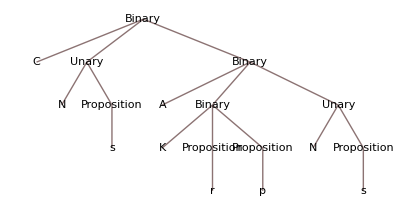

```mathematica
TreeForm@$p@"CNsAKrpNs"
```

Using Jabelean’s solver (in JacquardSolver.m)

```mathematica
KB={
rl[{},$p@"CNsAKrpNs"],
rl[{},$p@"CNCrpKNpAsr"],
rl[{},$p@"CCpsCCsrCpr"],
rl[{},$p@"CsCKpNsANqs"],
rl[{Binary["C",var[l],var[r]],var[l]},var[r]]
};
```

```mathematica
prettifySolutions[solnss_]:=
gridRules@(
(solns↦
(soln↦soln⟦1⟧->$u@soln⟦2⟧)/@
solns)/@
solnss)
```

This next directly answers 2 on page 90.

```mathematica
Solutions[Binary["C",var[x],$p@"AKrpNs"],KB]
```

{{var[x]→Unary[N,Proposition[s]]}}

```mathematica
prettifySolutions@Solutions[Binary["C",var[x],$p@"AKrpNs"],KB]
```

var | x | Ns

It’s not able to dig inside terms looking for an A:

```mathematica
prettifySolutions@Solutions[Binary["A",var[x],var[y]],KB]
```

#### Experiment with Cabrera’s solver

```mathematica
ClearAll[Knowledge,Statements];
SetAttributes[Statements,{Flat,Orderless}]
Knowledge=Statements[
$p@"CNsAKrpNs",
$p@"CNCrpKNpAsr",
$p@"CCpsCCsrCpr",
$p@"CsCKpNsANqs"
];
$u/@Question[Knowledge, Binary["C",X_,$p@"AKrpNs"], X]
```

{Ns}

A limitation of Cabrera’s solver is that it eagerly expands rules into facts, explosively, perhaps even infinitely, consuming memory. Until we make this lazy, we’ll use Jabelean’s solver, which is slower than Cabrera’s because it does not use Mathematica’s pattern matching.

#### Back to Jabelean’s solver

This next shows that the solver is bi-directional:

```mathematica
prettifySolutions@
Solutions[Binary["C",$p@"Ns",var[y]],KB]
```

var | y | AKrpNs

The next two show similar solutions for different L and R terms in a CLR.

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],$p@"KNpAsr"],KB]
```

var | x | NCrp

```mathematica
prettifySolutions@
Solutions[Binary["C",$p@"NCrp",var[y]],KB]
```

var | y | KNpAsr

#### Example 8 (3 on page 90 of Wff-n-Proof)

Can we find a CLR given an L and an R?

We can find all CLRs in the fact base, then filter them down to the ones that match our given L and R. We’ll do the filtering with a post-processing phase, to the solver. The solver’s job is to give us all CLRs in the fact base.

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | Cps
var | y | CCsrCpr
var | x | s
var | y | CKpNsANqs
var | x | NCrp
var | y | KNpAsr
var | x | Ns
var | y | AKrpNs

```mathematica
select[L_String,R_String]:=
soln↦
Select[soln,
rules↦
$u@(var[x]/.rules)===L&&
$u@(var[y]/.rules)===R]
```

```mathematica
prettifySolutions@
select["NCrp","KNpAsr"]@Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | NCrp
var | y | KNpAsr

We can also do it much faster and shorter by the direct but “out-of-the-box” pseudo-inference rule CoR:

```mathematica
And[$p@"NCrp",$p@"KNpAsr"]/.CoR//$u
```

CNCrpKNpAsr

#### Page 91 of Wff-n-Proof

The first one is a proper application of the true inference rule Co:

```mathematica
And[$p@"CKNprs",$p@"KNpr"]/.Co//$u
```

s

The second one requires a solution, that is, finding a CLR and L that would imply R

```mathematica
prettifySolutions@
select["Cps","CCsrCpr"]@
Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | Cps
var | y | CCsrCpr

Or writing it all out

```mathematica
(Binary["C",var[x],var[y]]/.
(select["Cps","CCsrCpr"]@
Solutions[Binary["C",var[x],var[y]],KB])⟦1⟧)//
$u
```

CCpsCCsrCpr

We can do the same with the bogus pseudorule CoR

```mathematica
And[
$p@"Cps",
$p@"CCsrCpr"]/.CoR//$u
```

CCpsCCsrCpr

The third one also requires a solution:

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],$p@"CKpNsANqs"],KB]
```

var | x | s

or an application of the bogus pseudorule CoL

```mathematica
And[
$p@"CsCKpNsANqs",
$p@"CKpNsANqs"]/.CoL//$u
```

s

### Proofs (page 92 ff)

```mathematica
ClearAll[inferStep,writeStep,writeProof];
inferStep[truths_,premise_?AtomQ,rule_]:=(truths⟦premise⟧)/.rule;
inferStep[truths_,premises_,rule_]:=truths⟦#⟧&/@premises/.rule;
SetAttributes[writeStep,HoldAll];
writeStep[truths_,{piPair:{premise_,rule_}}]:=
$u/@Append[truths,inferStep[truths,premise,rule]];
writeStep[truths_,{piPair:{premise_,rule_},morePairs__}]:=
writeStep[Append[truths,inferStep[truths,premise,rule]],{morePairs}];
SetAttributes[writeProof,HoldAll];
writeProof[suppositions_List,pairs_List]:=
writeStep[$p/@suppositions,pairs];
```

#### P1 -- page 92

```mathematica
writeProof[{"Cpr","Kpq"},{{2,KoL},{1&&3,Co}}]
```

{Cpr,Kpq,p,r}

#### P2 -- page 93

```mathematica
writeProof[{"p","KsCpr"},{{2,KoL},{2,KoR},{4&&1,Co},{3&&5,Ki}}]
```

{p,KsCpr,s,Cpr,r,Ksr}

#### P3 -- page 93

```mathematica
writeProof[{"p","Crs","Cpr"},{{3&&1,Co},{2&&4,Co},{1&&5,Ki}}]
```

{p,Crs,Cpr,r,s,Kps}

#### P4 -- page 93

```mathematica
writeProof[{"KsCNqNr","Csp","CpNq"},{{1,KoL},{2&&4,Co},{3&&5,Co},{1,KoR},{7&&6,Co}}]
```

{KsCNqNr,Csp,CpNq,s,p,Nq,CNqNr,Nr}

#### P5 -- page 93

```mathematica
writeProof[{"Kpq","Cpr","Cqs"},{
{1,KoL},
{2&&4,Co},
{1,KoR},
{3&&6,Co},
{5&&7,Ki}}]
```

{Kpq,Cpr,Cqs,p,r,q,s,Krs}

#### P6 -- page 94

```mathematica
writeProof[{"KpCqr","KCsqCps"},{
{1,KoL},
{2,KoR},
{4&&3,Co},
{2,KoL},
{6&&5,Co},
{1,KoR},
{8&&7,Co}}]
```

{KpCqr,KCsqCps,p,Cps,s,Csq,q,Cqr,r}

#### P7 -- page 94

```mathematica
writeProof[{"CpKqCsr","KpCqs"},{
{2,KoL},
{1&&3,Co},
{4,KoL},
{2,KoR},
{6&&5,Co},
{4,KoR},
{8&&7,Co}}]
```

{CpKqCsr,KpCqs,p,KqCsr,q,Cqs,s,Csr,r}

#### P8 -- page 95

```mathematica
writeProof[{"KpCKpqr","Kqs"},{
{1,KoL},
{2,KoL},
{3&&4,Ki},
{1,KoR},
{6&&5,Co},
{2,KoR},
{7&&8,Ki}}]
```

{KpCKpqr,Kqs,p,q,Kpq,CKpqr,r,s,Krs}

#### P9 -- page 95

```mathematica
writeProof[{"CpCqCrs","Kpq","r"},{
{2,KoL},
{1&&4,Co},
{2,KoR},
{5&&6,Co},
{7&&3,Co},
{8&&3,Ki}
}]
```

{CpCqCrs,Kpq,r,p,CqCrs,q,Crs,s,Ksr}

#### P10 -- page 95

Now do a little more to make them pretty:

```mathematica
Zip[
Range[10],
writeProof[{"KsCsq","CqCsr"},{
{1,KoL},
{1,KoR},
{4&&3,Co},
{2&&5,Co},
{6&&3,Co}}],
List]//MatrixForm
```

(1 | KsCsq
2 | CqCsr
3 | s
4 | Csq
5 | q
6 | Csr
7 | r)

#### Page 101 -- need to modify write-proof to handle symbolic indices

```mathematica
Zip[
Range[10],
writeProof[{"Kqp"},{{1,KoL},{1,KoR},{2&&3,Ki},{1:>4,Ci}}],
List
]//MatrixForm
```

(1 | Kqp
2 | q
3 | p
4 | Kqp
5 | CKqpKqp)

Format a truth as a quadruple of an index, a premise form -- a combination of indices, a rule, and an output. A step consists in writing a new truth into the table of truths.

```mathematica
ClearAll[inferStep2,writeStep2,writeProof2];
```

```mathematica
InferenceRuleNames[Supp]="Supp";
inferStep2[truths_,premise_?AtomQ,rule_]:=(truths[premise]⟦4⟧)/.rule;
inferStep2[truths_,premises_,rule_]:=truths[#]⟦4⟧&/@premises/.rule;
SetAttributes[writeStep2,HoldAll];
writeStep2[truths_,{triple:{index_,premise_,rule_,commentary___}}]:=
(truths[index]=Append[triple⟦1;;3⟧(* discard commentary *),inferStep2[truths,premise,rule]];
Module[{d=DownValues[truths]},
{#⟦2,1⟧,$u@#⟦2,4⟧,#⟦2,2⟧,InferenceRuleNames[#⟦2,3⟧]}&/@d//MatrixForm]);
writeStep2[truths_,{triple:{index_,premise_,rule_,commentary___},more__}]:=
(truths[index]=Append[triple⟦1;;3⟧(* discard commentary *),inferStep2[truths,premise,rule]];
writeStep2[truths,{more}]);
SetAttributes[writeProof2,HoldAll];
writeProof2[supps_List,triples_List]:=
Module[{truths},
Map[
s↦truths[s⟦1⟧]={s⟦1⟧,s⟦1⟧,Supp,$p@s⟦2⟧},supps];
writeStep2[truths,triples]];
```

#### P1 -- page 101, written prettily

```mathematica
writeProof2[{{"1a","Kqp"}},{
{"1b","1a",KoL},
{"1c","1a",KoR},
{"1d","1c"&&"1b",Ki},
{"2","1a":>"1d",Ci}}]
```

(1a | Kqp | 1a | Supp
1b | q | 1a | KoL
1c | p | 1a | KoR
1d | Kpq | 1c&&1b | Ki
2 | CKqpKpq | 1a:>1d | Ci)

#### P8 -- page 95, even prettier

```mathematica
writeProof2[{{1,"KpCKpqr"},{2,"Kqs"}},{
{3,1,KoL},
{4,2,KoL},
{5,3&&4,Ki},
{6,1,KoR},
{7,6&&5,Co},
{8,2,KoR},
{9,7&&8,Ki}}]
```

(1 | KpCKpqr | 1 | Supp
2 | Kqs | 2 | Supp
3 | p | 1 | KoL
4 | q | 2 | KoL
5 | Kpq | 3&&4 | Ki
6 | CKpqr | 1 | KoR
7 | r | 6&&5 | Co
8 | s | 2 | KoR
9 | Krs | 7&&8 | Ki)

#### P9 -- page 95, even prettier

```mathematica
writeProof2[{{1,"CpCqCrs"},{2,"Kpq"},{3,"r"}},{
{4,2,KoL},
{5,1&&4,Co},
{6,2,KoR},
{7,5&&6,Co},
{8,7&&3,Co},
{9,8&&3,Ki}
}]
```

(1 | CpCqCrs | 1 | Supp
2 | Kpq | 2 | Supp
3 | r | 3 | Supp
4 | p | 2 | KoL
5 | CqCrs | 1&&4 | Co
6 | q | 2 | KoR
7 | Crs | 5&&6 | Co
8 | s | 7&&3 | Co
9 | Ksr | 8&&3 | Ki)

#### P10 -- page 95, even prettier

```mathematica
writeProof2[{{1,"KsCsq"},{2,"CqCsr"}},{
{3,1,KoL},
{4,1,KoR},
{5,4&&3,Co},
{6,2&&5,Co},
{7,6&&3,Co}}]
```

(1 | KsCsq | 1 | Supp
2 | CqCsr | 2 | Supp
3 | s | 1 | KoL
4 | Csq | 1 | KoR
5 | q | 4&&3 | Co
6 | Csr | 2&&5 | Co
7 | r | 6&&3 | Co)

### Deeper Deductions

#### P2 -- page 103

```mathematica
writeProof2[{{"1a","q"},{"1b1","KrCrs"}},{
{"1b2","1b1",KoL},
{"1b3","1b1",KoR},
{"1b4","1b3"&&"1b2",Co},
{"1c","1b1":>"1b4",Ci},
{"2","1a":>"1c",Ci}
}]
```

(1a | q | 1a | Supp
1b1 | KrCrs | 1b1 | Supp
1b2 | r | 1b1 | KoL
1b3 | Crs | 1b1 | KoR
1b4 | s | 1b3&&1b2 | Co
1c | CKrCrss | 1b1:>1b4 | Ci
2 | CqCKrCrss | 1a:>1c | Ci)

#### P3 -- page 110

```mathematica
writeProof2[{
{"1a","Krs"}
},{
{"1b","1a",KoL},
{"1c","1a",KoL},
{"1d","1a",KoR},
{"1e","1b"&&"1c",Ki},
{"1f","1d"&&"1e",Ki},
{"2","1a":>"1f",Ci}
}]
```

(1a | Krs | 1a | Supp
1b | r | 1a | KoL
1c | r | 1a | KoL
1d | s | 1a | KoR
1e | Krr | 1b&&1c | Ki
1f | KsKrr | 1d&&1e | Ki
2 | CKrsKsKrr | 1a:>1f | Ci)

#### P4 -- page 112

```mathematica
writeProof2[{
{"1a","KpCpq"}
},{
{"1b","1a",KoL},
{"1c","1a",KoR},
{"1d","1c"&&"1b",Co},
{"2","1a":>"1d",Ci}
}]
```

(1a | KpCpq | 1a | Supp
1b | p | 1a | KoL
1c | Cpq | 1a | KoR
1d | q | 1c&&1b | Co
2 | CKpCpqq | 1a:>1d | Ci)

Proper use of the Ci-practice form would require us to parse the names of the inferences in the first columns of the displays. All the items marked 1a through 1d in P4 above, for example, constitute a lemma (called a sub-proof in the game manual). Proper use of Ci in the game is to cite the lemma as justification, rather than to cite individual lines in it. For instance, in line 2 of P4 above, we should say “1” instead of “1a:>1d”. To implement such in our game would require introducing substructure into the naming of lines of inference. (UNDONE).

The following example illustrates even one more level of sub-structure.

Add another slot on each inference line for commentary.

#### P5 -- page 114

```mathematica
writeProof2[{
{"1a","q"},
{"1b1","Krp"}
},{
{"1b2","1b1",KoR,"p"},
{"1c","1b1":>"1b2",Ci,"CKrpp"},
{"2","1a":>"1c",Ci,"CqCKrpp"}
}]
```

(1a | q | 1a | Supp
1b1 | Krp | 1b1 | Supp
1b2 | p | 1b1 | KoR
1c | CKrpp | 1b1:>1b2 | Ci
2 | CqCKrpp | 1a:>1c | Ci)

#### P6 -- page 114

```mathematica
writeProof2[{
{"1a","KsCsr"}
},{
{"1b","1a",KoL,"s"},
{"1c","1a",KoR,"Csr"},
{"1d","1c"&&"1b",Co,"r"},
{"1e","1d"&&"1b",Ki,"Krs"},
{"1f","1b"&&"1e",Ki,"KsKrs"},
{"2","1a":>"1f",Ci,"CKsCsrKsKrs"}
}]
```

(1a | KsCsr | 1a | Supp
1b | s | 1a | KoL
1c | Csr | 1a | KoR
1d | r | 1c&&1b | Co
1e | Krs | 1d&&1b | Ki
1f | KsKrs | 1b&&1e | Ki
2 | CKsCsrKsKrs | 1a:>1f | Ci)

#### P7 -- page 116 --> CCCKpqprr

```mathematica
writeProof2[{
{"1a","CCKpqpr"},
{"1b1","Kpq"}
},{
{"1b2","1b1",KoL,"p"},
{"1c","1b1":>"1b2",Ci,"CKpqp"},
{"1d","1a"&&"1c",Co,"r"},
{"2","1a":>"1d",Ci,"CCCKpqprr"}
}]
```

(1a | CCKpqpr | 1a | Supp
1b1 | Kpq | 1b1 | Supp
1b2 | p | 1b1 | KoL
1c | CKpqp | 1b1:>1b2 | Ci
1d | r | 1a&&1c | Co
2 | CCCKpqprr | 1a:>1d | Ci)

#### P8 -- page 116 --> CApqCNpCKrsr

The pattern emerging is that every time I see a C, I am going to nest a level in my proof structure. The new level is a lemma that assumes the premise and tries independently to prove the consequent of the C.

```mathematica
writeProof2[{
{"1a","Apq"},
{"1b1","Np"},
{"1b2a","Ksr"}
},{
{"1b2b","1b2a",KoR,"r"},
{"1b3","1b2a":>"1b2b",Ci,"CNpCKrsr"},
{"1c","1b1":>"1b3",Ci,"CnpCKrsr"},
{"2","1a":>"1c",Ci,"CApqCNpCKrsr"}
}]
```

(1a | Apq | 1a | Supp
1b1 | Np | 1b1 | Supp
1b2a | Ksr | 1b2a | Supp
1b2b | r | 1b2a | KoR
1b3 | CKsrr | 1b2a:>1b2b | Ci
1c | CNpCKsrr | 1b1:>1b3 | Ci
2 | CApqCNpCKsrr | 1a:>1c | Ci)

#### P9 -- page 116 --> CNsCNpCsCKrCrqq

```mathematica
writeProof2[{
{"1a","Ns"},
{"1b1","Np"},
{"1b2a","s"},
{"1b2b1","KrCrq"}
},{
{"1b2b2","1b2b1",KoL,"r"},
{"1b2b3","1b2b1",KoR,"Crq"},
{"1b2b4","1b2b2"&&"1b2b3",Co,"q"},
{"1b2c","1b2b1":>"1b2b4",Ci,"CKrCrqq -- lemma"},
{"1b3","1b2a":>"1b2c",Ci,"CsCKrCrqq -- lemma"},
{"1c","1b1":>"1b3",Ci,"CNpCsCKrCrqq -- lemma"},
{"2","1a":>"1c",Ci}
}]
```

(1a | Ns | 1a | Supp
1b1 | Np | 1b1 | Supp
1b2a | s | 1b2a | Supp
1b2b1 | KrCrq | 1b2b1 | Supp
1b2b2 | r | 1b2b1 | KoL
1b2b3 | Crq | 1b2b1 | KoR
1b2b4 | q | 1b2b2&&1b2b3 | Co
1b2c | CKrCrqq | 1b2b1:>1b2b4 | Ci
1b3 | CsCKrCrqq | 1b2a:>1b2c | Ci
1c | CNpCsCKrCrqq | 1b1:>1b3 | Ci
2 | CNsCNpCsCKrCrqq | 1a:>1c | Ci)

#### P10 -- page 117 --> CpCqCNqCNpCKCrsrs

At this point, I am using the proof machinery as fancy pencil-and-paper layout. It’s not actually doing any checking, structuring, or destructuring for me, just straight lookup and substitution. I’m doing the proofs; it’s just writing them out for me in a pretty format.

Rhetorically, this is an interesting case. We pose conditionals that alternately presume q and Nq, p and Np and derive a true statement that if some final conditional, Crs, and its premise, r, then then its consequent, s. A listener to a real argument structured this way might hear that some contradiction resulted in an independent truth. But, there is no contradiction because everything was conditional and the final result, CKCrsrs, did not depend on p and q, the alternating premises.

```mathematica
writeProof2[{
{"1a","p"},
{"1b1","q"},
{"1b2a","Nq"},
{"1b2b1","Np"},
{"1b2b2a","KCrsr"}
},{
{"1b2b2b","1b2b2a",KoR,"r"},
{"1b2b2c","1b2b2a",KoL,"Crs"},
{"1b2b2d","1b2b2b"&&"1b2b2c",Co,"s"},
{"1b2b3","1b2b2a":>"1b2b2d",Ci,"CKCrsrs"},
{"1b2c","1b2b1":>"1b2b3",Ci,"CNpCKCrsrs"},
{"1b3","1b2a":>"1b2c",Ci,"CNqCNpCKCrsrs"},
{"1c","1b1":>"1b3",Ci,"CqCNqCNpCKCrsrs"},
{"2","1a":>"1c",Ci,"CpCqCNqCNpCKCrsrs"}
}]
```

(1a | p | 1a | Supp
1b1 | q | 1b1 | Supp
1b2a | Nq | 1b2a | Supp
1b2b1 | Np | 1b2b1 | Supp
1b2b2a | KCrsr | 1b2b2a | Supp
1b2b2b | r | 1b2b2a | KoR
1b2b2c | Crs | 1b2b2a | KoL
1b2b2d | s | 1b2b2b&&1b2b2c | Co
1b2b3 | CKCrsrs | 1b2b2a:>1b2b2d | Ci
1b2c | CNpCKCrsrs | 1b2b1:>1b2b3 | Ci
1b3 | CNqCNpCKCrsrs | 1b2a:>1b2c | Ci
1c | CqCNqCNpCKCrsrs | 1b1:>1b3 | Ci
2 | CpCqCNqCNpCKCrsrs | 1a:>1c | Ci)

### Reiteration -- page 119ff

```mathematica
DefineInferenceRule[R,left_:>left];
```

```mathematica
writeProof2[{
{"1","CKpqr"},
{"2a","p"},
{"2c1","q"}
},{
{"2b","1",R,"CKpqr"},
{"2c2","2a",R,"p"}
}]
```

(1 | CKpqr | 1 | Supp
2a | p | 2a | Supp
2b | CKpqr | 1 | R
2c1 | q | 2c1 | Supp
2c2 | p | 2a | R)

Do a better job of laying out proofs; page 122ff

```mathematica
{{"1", "CKpqr", "s"}, {"2", □, □}}
```

{{1,CKpqr,s},{2,□,□}}

```mathematica
%//FullForm
```

List[List["1","CKpqr","s"],List["2",\[Placeholder],\[Placeholder]]]

```mathematica
%%
```

{{1,CKpqr,s},{2,□,□}}

```mathematica
{{"1","CKpqr","s"},{"2",□,□}}
```

{{1,CKpqr,s},{2,□,□}}

Here’s an approach to the sequences, but it creates difficulties for the justifications.

```mathematica
Grid[{
(*{"P1","CKpqr -> CpCqr"},*)
{Grid[{
{"1","CKpqr"},
{"2",Grid[{
{"a","p"},
{"b","CKpqr"},
{"c",Grid[{
{"1","q"},
{"2","p"},
{"3","Kpq"},
{"4","CKpqr"},
{"5","r"}
},Frame->All]},
{"d","Cqr"}
},Frame->All]},
{"3","CpCqr"}
},Frame->All]}
},Frame->All]
```

1 | CKpqr
2 | a | p
b | CKpqr
c | 1 | q
2 | p
3 | Kpq
4 | CKpqr
5 | r
d | Cqr
3 | CpCqr

Suppose we know at the outset how many levels of nesting we need. we can then use SpanFromLeft to leave judicious spacing.

```mathematica
sl=SpanFromLeft
```

```mathematica
{{"1", "CKpqr", sl, sl, "s"}, {"2", "a", "p", sl, "s"}, {sl, "b", "CKqpr", sl, "1,R"}, {sl, "c", "1", "q", "s"}, {sl, sl, "2", "p", "a,R"}, {sl, sl, "3", "Kpq", "2,1,Ki"}, {sl, sl, "4", "CKpqr", "b,R"}, {sl, sl, "5", "r", "4,3,Co"}, {sl, "d", "Cqr", sl, "c,Ci"}, {"3", "CpCqr", sl, sl, "2,Ci"}}//Grid[#,Frame->All]&
```

1 | CKpqr |  |  | s
2 | a | p |  | s
 | b | CKqpr |  | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d | Cqr |  | c,Ci
3 | CpCqr |  |  | 2,Ci

```mathematica
{{"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"", "b", sl, "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"2", "b", sl, "CKqpr", "1,R"}, {"2", "c", "1", "q", "s"}, {"2", "c", "2", "p", "a,R"}, {"2", "c", "3", "Kpq", "2,1,Ki"}, {"2", "c", "4", "CKpqr", "b,R"}, {"2", "c", "5", "r", "4,3,Co"}, {"2", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
2 | b |  | CKqpr | 1,R
2 | c | 1 | q | s
2 | c | 2 | p | a,R
2 | c | 3 | Kpq | 2,1,Ki
2 | c | 4 | CKpqr | b,R
2 | c | 5 | r | 4,3,Co
2 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", , , "CKpqr", "s"}, {"2", "a", , "p", "s"}, {"2", "b", , "CKqpr", "1,R"}, {"2", "c", "1", "q", "s"}, {"2", "c", "2", "p", "a,R"}, {"2", "c", "3", "Kpq", "2,1,Ki"}, {"2", "c", "4", "CKpqr", "b,R"}, {"2", "c", "5", "r", "4,3,Co"}, {"2", "d", , "Cqr", "c,Ci"}, {"3", , , "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
2 | b |  | CKqpr | 1,R
2 | c | 1 | q | s
2 | c | 2 | p | a,R
2 | c | 3 | Kpq | 2,1,Ki
2 | c | 4 | CKpqr | b,R
2 | c | 5 | r | 4,3,Co
2 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", , , "CKpqr", "s"}, {"2", "a", , "p", "s"}, {"", "b", , "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", , "Cqr", "c,Ci"}, {"3", , , "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
sa=SpanFromAbove;sb=SpanFromBoth;
```

```mathematica
{{"P1", sl, sl, "CpCqr", "CKpqr"}, {sa, sb, sb, sa, sa}, {"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"", "b", sl, "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

P1 |  |  | CpCqr | CKpqr
 |  |  |  | 
1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

There’s the pattern I like best. How to get that from a sequence of proofs and sub-proofs?

Perhaps automating the layout is overkill. Let’s focus on filling in the content.

The numbers / letters / keys for application of rule R refer to one level out. The keys for application of other rules refer to the current level.

## ALGEBRA-1 EXPRESSIONS

```mathematica
ClearAll[F]; (* for "Field" *)
F[Expr]=({{FSum}, {FProd}, {FVar}, {FInt}});(* "Sum" collides with a built-in. *)
F[FSum]={{Plus,Expr,Expr}}; (* Do we want the built-in "Plus"? *)
F[FInt]={{RandomInteger}};
F[FVar]={
(*{a},{b},{c},{d},{e},{f},{g},{h},{i},{j},{k},{m},{n},*)
{x},{y},{z},{-x},{-y},{-z},{1/x},{1/y},{1/z}
(*,{u},{v},{w},{p},{q},{r},{s},{t}*)};
F[FProd]={{Times,Expr,Expr}};
F[Start]={{Expr}};
```

```mathematica
visGrammar@F
```

Expr | FSum
FProd
FVar
FInt
FInt | RandomInteger
FProd | Times
Expr
Expr
FSum | Plus
Expr
Expr
FVar | x
y
z
Times | -1 | x
Times | -1 | y
Times | -1 | z
Power | x | -1
Power | y | -1
Power | z | -1
Start | Expr

```mathematica
(FProbabilized=injectGenerationProbabilities[F,
Function[list,
If[list==={{FSum},{FProd}},{.5,.5},
equiProbabilities@list]]
])//visGrammar
```

Expr | probability | 0.25
alternative | FSum
probability | 0.25
alternative | FProd
probability | 0.25
alternative | FVar
probability | 0.25
alternative | FInt
FInt | probability | 1.
alternative | RandomInteger
FProd | probability | 1.
alternative | Times
Expr
Expr
FSum | probability | 1.
alternative | Plus
Expr
Expr
FVar | probability | 0.111111
alternative | x
probability | 0.111111
alternative | y
probability | 0.111111
alternative | z
probability | 0.111111
alternative | Times | -1 | x
probability | 0.111111
alternative | Times | -1 | y
probability | 0.111111
alternative | Times | -1 | z
probability | 0.111111
alternative | Power | x | -1
probability | 0.111111
alternative | Power | y | -1
probability | 0.111111
alternative | Power | z | -1
Start | probability | 1.
alternative | Expr

```mathematica
ClearAll[$exprTable];
parserPatterns[F,$exprTable];
```

```mathematica
DynamicModule[{foo},
Manipulate[foo,Button["GEN",foo=
((generateSentence[FProbabilized,FVar,terminalsFromGrammar@F,10]//InputForm))]]]
```

```mathematica
ClearAll[$fexpr];
$fexpr[dummy_,depth_:20]:=
With[{sen=generateSentence[
FProbabilized,FVar,terminalsFromGrammar@F,depth]},
With[{parse=($exprTable@sen)[[2]]},
With[{interp={
FInt[RandomInteger]:>RandomInteger[10],
FVar->Identity,
(FSum|FProd)[f_,args__]:>Apply[f,{args}]}},
{TreeForm[parse,VertexLabeling->Automatic],(parse//.interp//FullSimplify)}]]]
```

```mathematica
$fcontender=0;
Animate[
Module[{t,e},
{t,e}=$fexpr[dummy];
With[{le=LeafCount[e]},
If[le>LeafCount@$fcontender,$fcontender=e];
Grid[{{e,SpanFromLeft},{le,t}},Frame->All]]],
{dummy,1,25,1}]
```

```mathematica
Dynamic[$fcontender]
```

```mathematica
DynamicModule[{foo},
Manipulate[foo,Button["GEN",foo=$fexpr[]]]]
```

## DEEPER EXAMPLE: BENPIERCE TYPES

Encode types from Benjamin C. Pierce’s book, TPL or “Types and Programming Languages.”

Call the grammar “BPT,” for “Ben Pierce Terms,” from Section 3.1 of his book. It has ONE non-terminal symbol. He calls it “t.” That’s too small for us. We’ll call it “Term.”

## UNTYPED UTTERANCES

Consistent with Sections 3.2 and 4.1 of TPL.

BP’s Ternary if foo then bar else baz is not in Polish prefix form. Prefix form would be if foo bar baz, much easier to parse with our nearly-trivial tools. Go there, because the point of this exercise is not to spend time on parsing, but to spend time on types.

```mathematica
ClearAll[BPT,Term,Ternary,Unary,BPTtokens];
BPT[Term]=({{Const}, {Ternary}, {Unary}});
BPT[Const]=({{"true"}, {"false"}, {"0"}}); (* groundTerm for travesties *)
(* incovenient to parse with present tools *)
(*BPT[Ternary]={{"if",Term,"then",Term,"else",Term}};*)
BPT[Ternary]={{"if", Term, Term,Term}};
BPT[Unary]=({{"succ", Term}, {"pred", Term}, {"iszero", Term}});
BPT[Start]={{Term}};
```

from Section 4.1:

```mathematica
ClearAll[isnumerical];
isnumerical[Const["0"]]:=True;
isnumerical[Unary["succ",t1_]]:=isnumerical@t1;
isnumerical[_]:=False;

ClearAll[isval];
isval[Const["true"]]:=True;
isval[Const["false"]]:=True;
isval[t_?isnumerical]:=True;

isval[Const["0"]]
```

True

```mathematica
ClearAll[visGrammar];
visGrammar[g_]:=Module[{d=DownValues[g]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules;
visGrammar[BPT]
```

Const | true
false
0
Start | Term
Term | Const
Ternary
Unary
Ternary | if
Term
Term
Term
Unary | succ
Term
pred
Term
iszero
Term

```mathematica
allSymbols@BPT//gridExpression
```

| 0
 | false
 | if
 | iszero
 | pred
List | succ
 | true
 | Const
 | Term
 | Ternary
 | Unary

```mathematica
ClearAll[$bptTable];
parserPatterns[BPT,$bptTable];
DownValues@$bptTable//TableForm
```

HoldPattern[$bptTable[{tok$19207:true|false|0,toks$19207___},tree$19207_:Null]]:>genParserBody[0,tok$19207,{toks$19207},Const,{},$bptTable]
HoldPattern[$bptTable[{},tree_:Null]]:>{{},tree}
HoldPattern[$bptTable[{tok$19211:Alternatives[if],toks$19211___},tree$19211_:Null]]:>genParserBody[3,tok$19211,{toks$19211},Ternary,{},$bptTable]
HoldPattern[$bptTable[{tok$19213:succ|pred|iszero,toks$19213___},tree$19213_:Null]]:>genParserBody[1,tok$19213,{toks$19213},Unary,{},$bptTable]
HoldPattern[$bptTable[xs$___]]:>Throw[{ToString[$bptTable]<>: CATASTROPHE: ,xs$}]

Generate some travesties from this grammar, BPT. Equiprobabilities doesn’t generate enough variety, so we’ll build a probability-assignment function up by hand.

```mathematica
??equiProbabilities
```

```mathematica
ClearAll[BPTprobabilities];
BPTprobabilities[list_List]:=If[list==={{Const},{Ternary},{Unary}},
{.25,.50,.25}, equiProbabilities@list];
```

```mathematica
(BPTprobabilized=injectGenerationProbabilities[BPT,BPTprobabilities])//visGrammar
```

Const | probability | 0.333333
alternative | true
probability | 0.333333
alternative | false
probability | 0.333333
alternative | 0
Start | probability | 1.
alternative | Term
Term | probability | 0.25
alternative | Const
probability | 0.5
alternative | Ternary
probability | 0.25
alternative | Unary
Ternary | probability | 1.
alternative | if
Term
Term
Term
Unary | probability | 0.333333
alternative | succ
Term
probability | 0.333333
alternative | pred
Term
probability | 0.333333
alternative | iszero
Term

```mathematica
ClearAll[spaceRules];
spaceRules={x_String:>x<>" "};
```

```mathematica
SeedRandom[26];
expressionStringFromSentence[generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,10],spaceRules]
```

pred iszero if 0 0 0

The parser, itself, is a composition of partTree (‘cadr’), the parser table above, and a tokenizer function, which will just be StringSplit for this application:

```mathematica
SeedRandom[26];
DynamicModule[{foo},
Manipulate[foo,
Button["GEN",foo=generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]]]]
```

In the display below, hover over a vertex to see its content.

```mathematica
SeedRandom[26];
DynamicModule[{foo},
Manipulate[{foo},
Button["GEN",foo=Module[{},
With[{sen=generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]},
With[{tpt=Timing@$bptTable@sen},
Column[{sen,
ToString[Length@sen]<>" Leaves",
ToString@tpt[[1]]*Seconds,
TreeForm[tpt[[2,2]](*,VertexLabeling->Automatic*),ImageSize->Large]},
Frame->All]]]]]]]
```

## SIZE AND DEPTH

## SMALL-STEP OPERATIONAL SEMANTICS

Gin up a sample.

```mathematica
SeedRandom[26];
ClearAll[$test];
($test=$bptTable[generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]][[2]])//InputForm
```

Unary["pred", Unary["iszero", Ternary["if", 
   Unary["iszero", Unary["pred", Ternary["if", Const["false"], 
      Const["false"], Const["true"]]]], Unary["iszero", 
    Ternary["if", Ternary["if", Const["false"], Const["false"], 
      Const["false"]], Const["false"], Const["0"]]], 
   Ternary["if", Ternary["if", Const["0"], Ternary["if", Const["0"], 
      Const["0"], Const["0"]], Const["0"]], Unary["iszero", 
     Ternary["if", Const["true"], Const["0"], Const["false"]]], 
    Ternary["if", Unary["succ", Const["0"]], Ternary["if", Const["0"], 
      Const["0"], Const["false"]], Ternary["if", Const["true"], Const["0"], 
      Const["false"]]]]]]]

### Boolean Evaluation Rules

```mathematica
ClearAll[Ternary,evBoolRules35];
(* model E-If with a function representing the premise transition that is above the line. The function returns the transition rules. *)
evBoolRules35[c1_,c1p_]:={
Ternary["if",Const["true"],t1_,t2_]:>t1,
Ternary["if",Const["false"],t1_,t2_]:>t2,
Ternary["if",c1,t1_,t2_]:>Ternary["if",c1p,t1,t2]};
(*Ternary["if",Const["true"],t1_,t2_]:=t1;
Ternary["if",Const["false"],t1_,t2_]:=t2;*)
ClearAll[dpyRules];
dpyRules={Const["0"]->"0",Const["true"]->"#t",Const["false"]->"#f"};
```

```mathematica
$test//.evBoolRules35[Null,Null]/.dpyRules
```

Unary[pred,Unary[iszero,Ternary[if,Unary[iszero,Unary[pred,#t]],Unary[iszero,0],Ternary[if,Ternary[if,0,Ternary[if,0,0,0],0],Unary[iszero,0],Ternary[if,Unary[succ,0],Ternary[if,0,0,#f],0]]]]]

```mathematica
Unary["pred",Unary["iszero",Ternary["if",Unary["iszero",Unary["pred","#t"]],Unary["iszero","0"],Ternary["if",Ternary["if","0",Ternary["if","0","0","0"],"0"],Unary["iszero","0"],Ternary["if",Unary["succ","0"],Ternary["if","0","0","#f"],"0"]]]]]
```

Unary[pred,Unary[iszero,Ternary[if,Unary[iszero,Unary[pred,#t]],Unary[iszero,0],Ternary[if,Ternary[if,0,Ternary[if,0,0,0],0],Unary[iszero,0],Ternary[if,Unary[succ,0],Ternary[if,0,0,#f],0]]]]]

```mathematica
Ternary["if",c1,t1,t2]//.evBoolRules35[c1,c1p]
```

Ternary[if,c1p,t1,t2]

The function for boolRules can be called with complicated arguments:.18

```mathematica
Ternary["if",Ternary["if",Const["true"],Const["false"],Const["true"]],t1,t2]//.evBoolRules35[Ternary["if",Const["true"],Const["false"],Const["true"]],c1p]
```

Ternary[if,c1p,t1,t2]

The following is the derivation tree of Section 3.5.3 in an manually prettified input form. But the output is clear.

```mathematica
Module[{s,t,u,if,$t,$f,rlz},
$t=Const["true"];$f=Const["false"];
if[a_,b_,c_]:=Ternary["if",a,b,c];
s=if[$t,$f,$f];
t=if[s,$t,$t];
u=if[$f,$t,$t];
rlz=evBoolRules35[t,u];
<|"s→false"->(
(s/.rlz)===$f),
"t→u"->
((t/.rlz)===u),
"(if t...)→(if u...)"->
((if[t,$f,$f]/.rlz)===if[u,$f,$f])
|>]
```

<|s→false→True,t→u→True,(if t...)→(if u...)→True|>

### Numerical Evaluation Rules

```mathematica
ClearAll[NB];
NB[Nv]=({{Zero}, {Succ}});
NB[Zero]={{"0"}};
NB[Succ]={{"succ",Nv}};
NB[Start]={{Nv}};
visGrammar[NB];
NBprobabilized=injectGenerationProbabilities[NB,equiProbabilities];
NBprobabilized//visGrammar;
generateSentence[NBprobabilized,Zero,terminalsFromGrammar@NB,20]
ClearAll[$nbTable];
parserPatterns[NB,$nbTable];
DownValues@$nbTable//TableForm;
```

{succ,0}

Some travesties on NB

```mathematica
DynamicModule[{foo},
Manipulate[foo,
Button["GEN",foo=($nbTable@generateSentence[NBprobabilized,Zero,terminalsFromGrammar@NB,40])[[2]]]]]
```

??? Cross the syntactic domain of BPT[Term] into the syntactic domain of NB[Nv].

```mathematica
ClearAll[evNumRules35];
evNumRules35[t1_,t1p_]:={
(*Const["0"]->Zero["0"],*)
Unary["pred",Const["0"]]:>Const["0"],
Unary["pred",Unary["succ",nv_]]:>nv,
Unary["iszero",Unary["succ",Const["succ"]]]:>Const["false"],
Unary["succ",t1]:>Unary["succ",t1p],
Unary["pred",t1]:>Unary["pred",t1p],
Unary["iszero",t1]:>Unary["iszero",t1p]
};
```

Above exercise 3.5.14:

```mathematica
Module[{rlz=evNumRules35[Null,Null],p,s,z,znv},
p[nv_]:=Unary["pred",nv];
z=Const["0"];
znv=Zero["0"];
s[nv_]:=Unary["succ",nv];
<|"p 0 → 0"->(p[z]/.rlz)==znv,
"s p 0 → s 0"->(s[p[z]]/.rlz)==s[z],
"p s p 0 → p s 0"->(p@s@p@z//.rlz)==(p@s@z/.rlz)|>]
```

<|p 0 → 0→Const[0]==Zero[0],s p 0 → s 0→True,p s p 0 → p s 0→True|>

## HORIZON SANDBOX

This is as far we got

### Can we automatically prove Wff-n-Proof’s “Derived rules of Inference”?

```mathematica
Rp=term_:>term;
```

```mathematica
And[w1,w1]/.Ci
```

w1&&w1

```mathematica
NNi=term_:>Unary["N",Unary["N",term]];
```

```mathematica
NNo=Unary["N",Unary["N",term_]]:>term;
```

The following is a DEEP Rabbit Hole (but nice!)

```mathematica
(* Needs["Theorema`"] *)
```

```mathematica
$Path
```

{/home/bcbeckman/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/12.2/SystemFiles/Links,/home/bcbeckman/.Mathematica/Kernel,/home/bcbeckman/.Mathematica/Autoload,/home/bcbeckman/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/bcbeckman,/usr/local/Wolfram/Mathematica/12.2/AddOns/Packages,/usr/local/Wolfram/Mathematica/12.2/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/12.2/AddOns/Autoload,/usr/local/Wolfram/Mathematica/12.2/AddOns/Applications,/usr/local/Wolfram/Mathematica/12.2/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/12.2/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/12.2/Documentation/English/System,/usr/local/Wolfram/Mathematica/12.2/SystemFiles/Data/ICC}